```mathematica
∑_(i=0)^n x^n/(n!)
```

((1+n) x^n)/(n!)

```mathematica
Expand[((1+n) x^n)/(n!)]
```

x^n/(n!)+(n x^n)/(n!)

```mathematica
∑_(i=0)^∞ x^n/(n!)
```

Sum::div: Sum does not converge.

∑_(i=0)^∞ x^n/(n!)

```mathematica
Limit[∑_(i=0)^a x^n/(n!),a->∞]
```

(x^n ∞)/(n!)

```mathematica
∑_(i=0)^n x^i/(n!)
```

(-1+x^(1+n))/((-1+x) n!)

```mathematica
∑_(i=0)^∞ x^i/(n!)
```

1/((1-x) n!)

```mathematica
∑_(i=0)^n x^i/(i!)
```

(ⅇ^x Gamma[1+n,x])/(n!)

```mathematica
∑_(i=0)^∞ x^i/(i!)
```

ⅇ^x

```mathematica
∑_(i=0)^∞ x^i
```

1/(1-x)

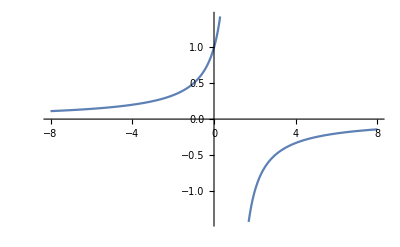

```mathematica
Plot[1/(1-x),{x,-8,8}]
```

```mathematica
∑_(i=0)^∞ x^(i n)
```

-1/(-1+x^n)

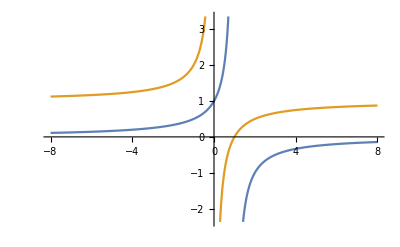

```mathematica
Plot[{1/(1-x),1/(1-(1/(1-x)))},{x,-8,8}]
```

```mathematica
1/(1-(1/(1-x)))
```

1/(1-1/(1-x))

```mathematica
Simplify[1/(1-1/(1-x))]
```

(-1+x)/x

```mathematica
FullSimplify[1/(1-1/(1-x)),x∈Reals]
```

(-1+x)/x

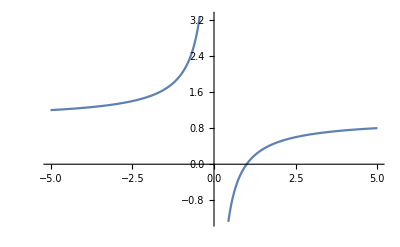

```mathematica
Plot[(-1+x)/x,{x,-5.01,5.01}]
```

```mathematica
1-x==-x+1
```

True

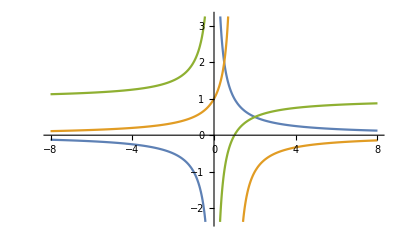

```mathematica
Plot[{1/x,1/(1-x),1/(1-(1/(1-x)))},{x,-8,8}]
```

```mathematica
1/x
```

1/x

```mathematica
1/(1/x)
```

x

```mathematica
1/(1/(1/x))
```

1/x

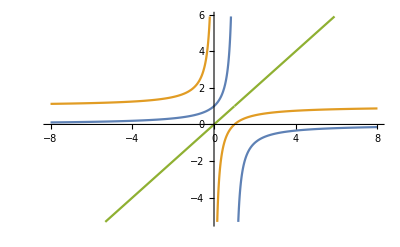

```mathematica
Plot[{1/(1-x),1/(1-(1/(1-x))),1/(1-(1/(1-(1/(1-x)))))},{x,-8,8}]
```

```mathematica
1/(1-(1/(1-(1/(1-x)))))
```

1/(1-1/(1-1/(1-x)))

```mathematica
Simplify[1/(1-1/(1-1/(1-x)))]
```

x

```mathematica
Nest[1/(1-#)&,x,2]
```

1/(1-1/(1-x))

```mathematica
Nest[1/(1-#)&,x,5]
```

1/(1-1/(1-1/(1-1/(1-1/(1-x)))))

```mathematica
NestList[1/#&,x,2]
```

{x,1/x,x}

```mathematica
NestList[1/#&,x,5]
```

{x,1/x,x,1/x,x,1/x}

```mathematica
NestList[1/(1-#)&,x,10]
```

{x,1/(1-x),1/(1-1/(1-x)),1/(1-1/(1-1/(1-x))),1/(1-1/(1-1/(1-1/(1-x)))),1/(1-1/(1-1/(1-1/(1-1/(1-x))))),1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-x)))))),1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-x))))))),1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-x)))))))),1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-x))))))))),1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-x))))))))))}

```mathematica
Attributes[Simplify]
```

{Protected}

```mathematica
Simplify/@NestList[1/(1-#)&,x,10]
```

{x,1/(1-x),(-1+x)/x,x,1/(1-x),(-1+x)/x,x,1/(1-x),(-1+x)/x,x,1/(1-x)}

```mathematica
FullForm[1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-x))))))))))]
```

Power[Plus[1,Times[-1,Power[Plus[1,Times[-1,Power[Plus[1,Times[-1,Power[Plus[1,Times[-1,Power[Plus[1,Times[-1,Power[Plus[1,Times[-1,Power[Plus[1,Times[-1,Power[Plus[1,Times[-1,Power[Plus[1,Times[-1,Power[Plus[1,Times[-1,x]],-1]]],-1]]],-1]]],-1]]],-1]]],-1]]],-1]]],-1]]],-1]]],-1]